# J42 Integral

### Parameters

```mathematica
(* a = 4 *)pbarRoot = {0.417909234928521,0.88953757977413,1.50313435358219,2.26227724679224,3.16916090818849,4.22598142237394,5.43520758590257,6.79968014734298,8.32267399714219,10.0079548106621,11.8598406971381,13.8832742150945,16.0839090039663,18.4682156066369,21.0436121723034,23.8186275692757,26.8031072000651,30.0084759187316,33.4480786375689,37.1376287337012,41.0958094224802,45.3450978234695,49.912922981558,54.8333423920613,60.1495575104923,65.9178564605306,72.2141398071796,79.1455059779102,86.8728427168776,95.6611504753672,106.017412544034,119.246074846868};

pbarWeight={0.00810350217768707,0.139349802695655,0.778927658209205,2.27068847781766,4.16201978678839,5.27788641670047,4.89485909244793,3.43717280920662,1.86904546196424,0.798763887000871,0.270852164829653,0.0732878795914489,0.01586714881709,0.00274947372013889,0.000380597860101854,4.19234411221472*10^-05,3.65309607883985*10^-06,2.49809512719197*10^-07,1.32687527252283*10^-08,5.40388315906601*10^-10,1.66054493087441*10^-11,3.77392781212211*10^-13,6.18757447978359*10^-15,7.09247603289048*10^-17,5.45950397697786*10^-19,2.67713699135924*10^-21,7.78642660507715*10^-24,1.21436823264902*10^-26,8.72951374350878*10^-30,2.25662022601836*10^-33,1.30979049102376*10^-37,5.18601511700047*10^-43};

GeVinversefm = 5.067731;

μBpts = 100;
Tpts = 100;

μBmin = 0.0;
μBmax = 4.06;
dμB=(μBmax-μBmin)/μBpts;
μBgrid=Table[μBmin+(i-1)*dμB,{i,1,μBpts+1}];

Tmin = 0.1;
Tmax = 0.82;
dT=(Tmax-Tmin)/Tpts;
Tgrid=Table[Tmin+(i-1)*dT,{i,1,Tpts+1}];
```

## Meson

### Pion

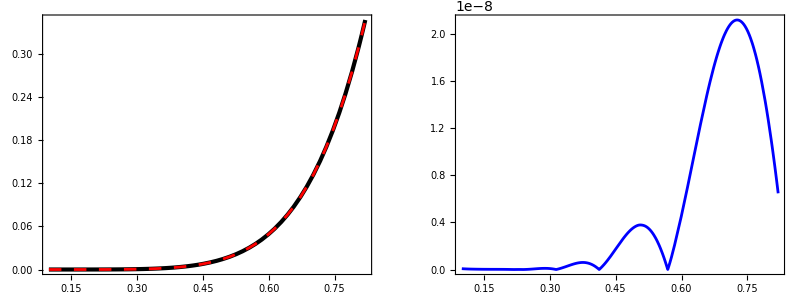

-Graphics-

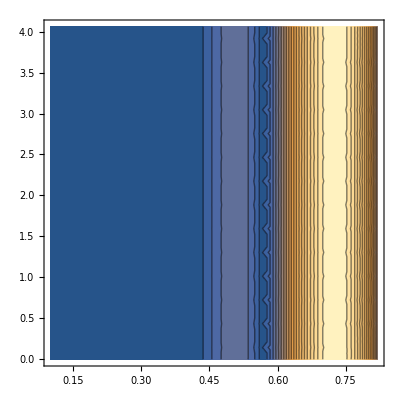

```mathematica
m = 0.140*GeVinversefm;
dof = 3.0; (* 3 mesons *)
θ=-1.0;
J42Integrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^6*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)]/((Exp[((pbar)^2+(m/T)^2)^(1/2)] +θ)^2));
J42GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)]/((Exp[((pbar)^2+(m/T)^2)^(1/2)] +θ)^2));
J42=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[J42Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*J42GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42=Interpolation[J42];
J42Gauss=Interpolation[J42Gauss];
GraphicsGrid[{{Plot[{J42[T,μBmin],J42Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmin]-J42Gauss[T,μBmin])/J42Gauss[T,μBmin]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{J42[T,μBmax],J42Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmax]-J42Gauss[T,μBmax])/J42Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

### Kaon

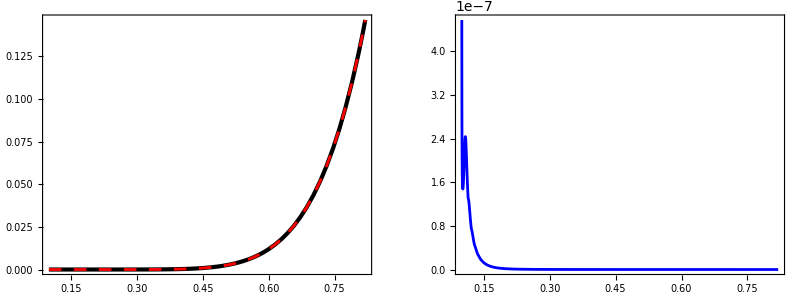

-Graphics-

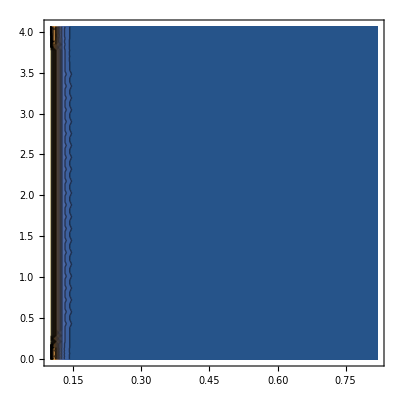

```mathematica
m = 0.50*GeVinversefm;
dof = 3.0; (* 3 kaons *)
θ=-1.0;
J42Integrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^6*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)]/((Exp[((pbar)^2+(m/T)^2)^(1/2)] +θ)^2));
J42GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)]/((Exp[((pbar)^2+(m/T)^2)^(1/2)] +θ)^2));
J42=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[J42Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*J42GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42=Interpolation[J42];
J42Gauss=Interpolation[J42Gauss];
GraphicsGrid[{{Plot[{J42[T,μBmin],J42Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmin]-J42Gauss[T,μBmin])/J42Gauss[T,μBmin]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{J42[T,μBmax],J42Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmax]-J42Gauss[T,μBmax])/J42Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

### Rho

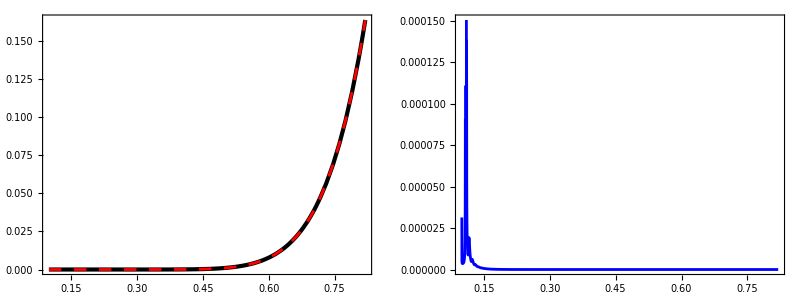

-Graphics-

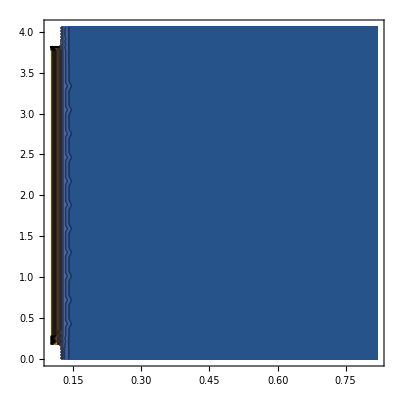

```mathematica
m = 0.77580*GeVinversefm;
dof = 9.0; (* 3 rhos * 3 spin states *)
θ=-1.0;
J42Integrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^6*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)]/((Exp[((pbar)^2+(m/T)^2)^(1/2)] +θ)^2));
J42GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)]/((Exp[((pbar)^2+(m/T)^2)^(1/2)] +θ)^2));
J42=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[J42Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*J42GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42=Interpolation[J42];
J42Gauss=Interpolation[J42Gauss];
GraphicsGrid[{{Plot[{J42[T,μBmin],J42Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmin]-J42Gauss[T,μBmin])/J42Gauss[T,μBmin]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{J42[T,μBmax],J42Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmax]-J42Gauss[T,μBmax])/J42Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

### f2-2010

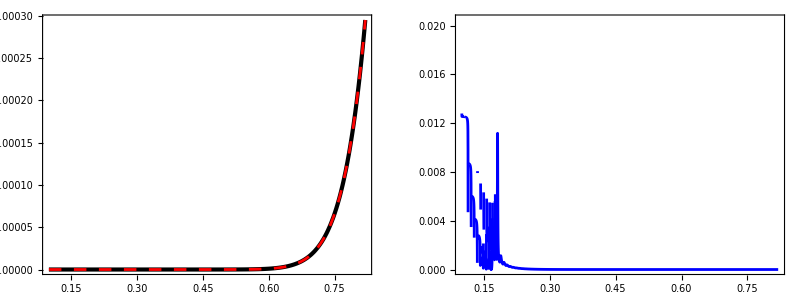

-Graphics-

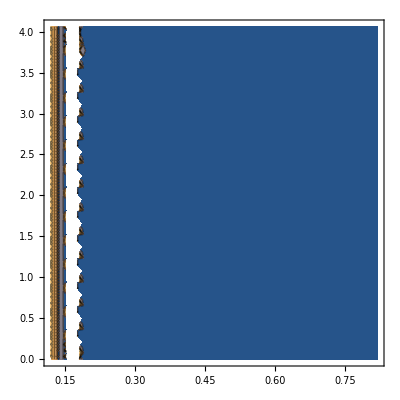

```mathematica
m =2.011*GeVinversefm;
dof = 5.0;
θ=-1.0;
J42Integrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^6*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)]/((Exp[((pbar)^2+(m/T)^2)^(1/2)] +θ)^2));
J42GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)]/((Exp[((pbar)^2+(m/T)^2)^(1/2)] +θ)^2));
J42=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[J42Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*J42GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42=Interpolation[J42];
J42Gauss=Interpolation[J42Gauss];
GraphicsGrid[{{Plot[{J42[T,μBmin],J42Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmin]-J42Gauss[T,μBmin])/J42Gauss[T,μBmin]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{J42[T,μBmax],J42Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmax]-J42Gauss[T,μBmax])/J42Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

## Baryon

### Proton

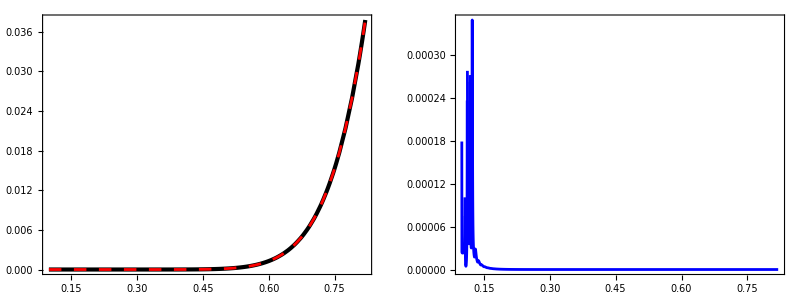

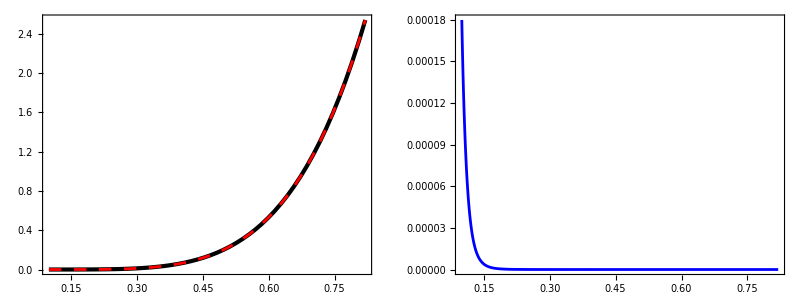

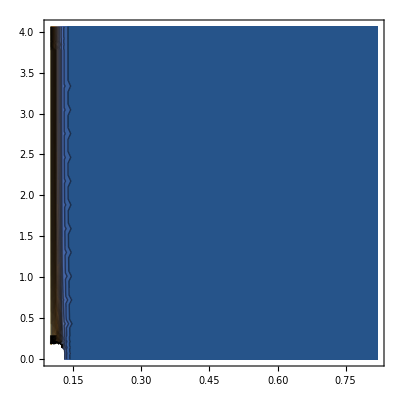

```mathematica
m = 0.938*GeVinversefm;
dof = 2.0;
θ=1.0;
J42Integrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^6*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
J42GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));

J42=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[J42Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*J42GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42=Interpolation[J42];
J42Gauss=Interpolation[J42Gauss];
GraphicsGrid[{{Plot[{J42[T,μBmin],J42Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmin]-J42Gauss[T,μBmin])/J42Gauss[T,μBmin]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{J42[T,μBmax],J42Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmax]-J42Gauss[T,μBmax])/J42Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

### Lambda

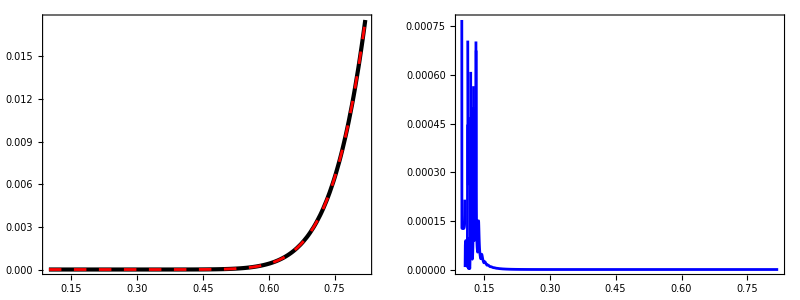

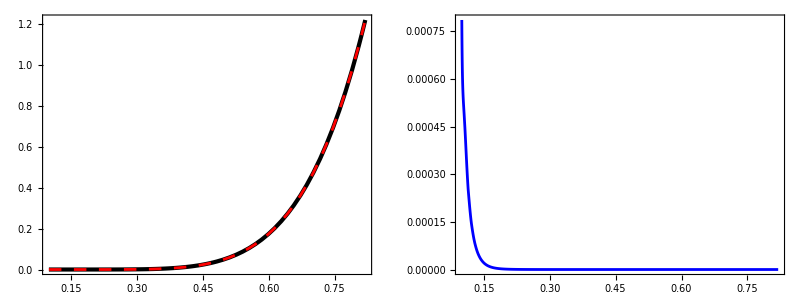

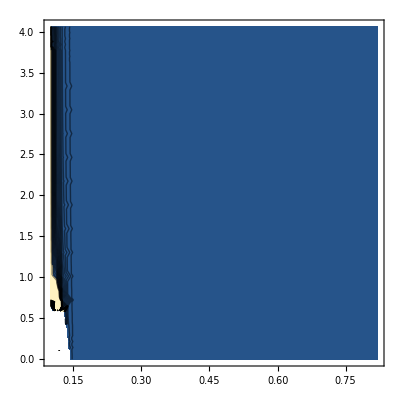

```mathematica
m = 1.11568*GeVinversefm;
dof = 2.0;
θ=1.0;
J42Integrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^6*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
J42GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));

J42=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[J42Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*J42GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42=Interpolation[J42];
J42Gauss=Interpolation[J42Gauss];
GraphicsGrid[{{Plot[{J42[T,μBmin],J42Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmin]-J42Gauss[T,μBmin])/J42Gauss[T,μBmin]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{J42[T,μBmax],J42Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmax]-J42Gauss[T,μBmax])/J42Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

### Omega

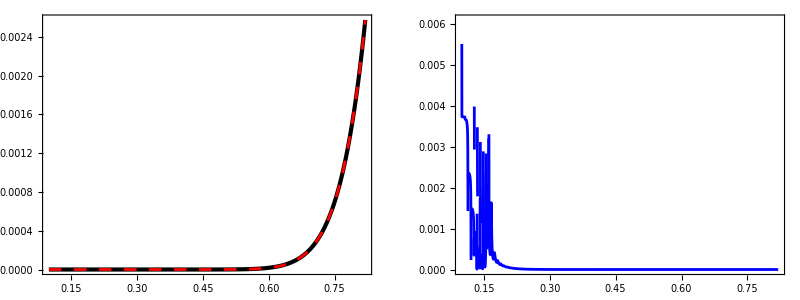

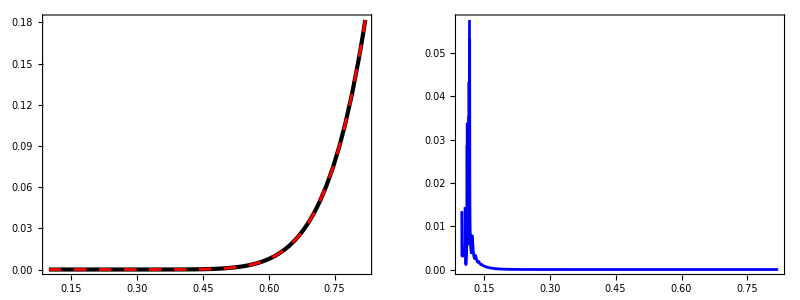

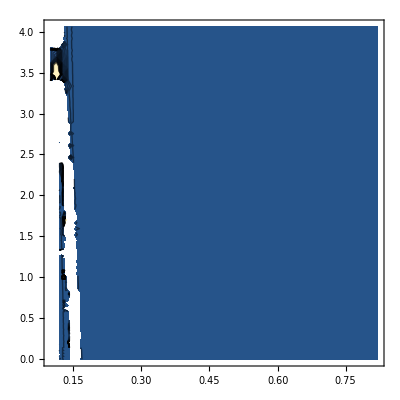

```mathematica
m = 1.67243*GeVinversefm;
dof = 4.0;
θ=1.0;
J42Integrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^6*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
J42GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));

J42=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[J42Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*J42GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42=Interpolation[J42];
J42Gauss=Interpolation[J42Gauss];
GraphicsGrid[{{Plot[{J42[T,μBmin],J42Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmin]-J42Gauss[T,μBmin])/J42Gauss[T,μBmin]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{J42[T,μBmax],J42Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmax]-J42Gauss[T,μBmax])/J42Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```

### Omega2250

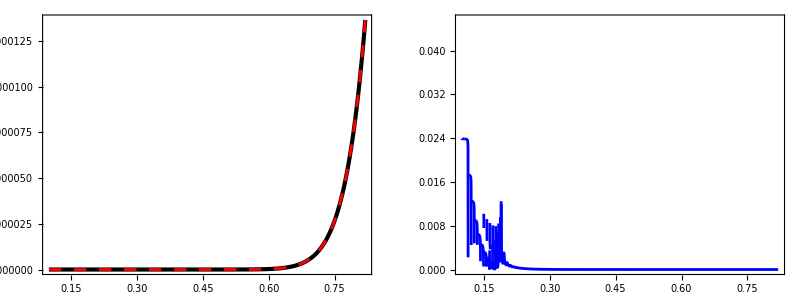

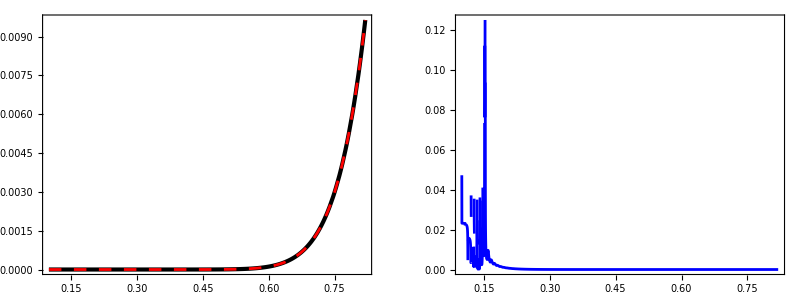

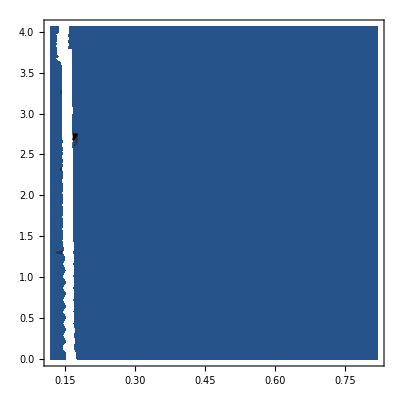

```mathematica
m = 2.25200*GeVinversefm;
dof = 4.0;
θ=1.0;
J42Integrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^6*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));
J42GaussIntegrand[T_,μB_,pbar_]:=(dof*(T)^6)/(30.0*Pi^2)*(pbar)^2*((pbar)^2+(m/T)^2)^(-1/2)*(Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)-μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)-μB/T] +θ)^2)+Exp[pbar+((pbar)^2+(m/T)^2)^(1/2)+μB/T]/((Exp[((pbar)^2+(m/T)^2)^(1/2)+μB/T]+θ )^2));

J42=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},NIntegrate[J42Integrand[Tgrid[[i]],μBgrid[[j]],pbar],{pbar,0,40}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42Gauss=Flatten[Table[{{Tgrid[[i]],μBgrid[[j]]},Sum[pbarWeight[[n]]*J42GaussIntegrand[Tgrid[[i]],μBgrid[[j]],pbarRoot[[n]]],{n,1,Length[pbarRoot]}]},{i,1,Length[Tgrid]},{j,1,Length[μBgrid]}],1];
J42=Interpolation[J42];
J42Gauss=Interpolation[J42Gauss];
GraphicsGrid[{{Plot[{J42[T,μBmin],J42Gauss[T,μBmin]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmin]-J42Gauss[T,μBmin])/J42Gauss[T,μBmin]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot[{J42[T,μBmax],J42Gauss[T,μBmax]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Black,AbsoluteThickness[3.]],Directive[Red,AbsoluteThickness[2],Dashing->Medium]},Frame->True],
Plot[{Abs[(J42[T,μBmax]-J42Gauss[T,μBmax])/J42Gauss[T,μBmax]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->{Directive[Blue,AbsoluteThickness[2]]},Frame->True]
}},ImageSize->{800,300}]
GraphicsGrid[{{Plot3D[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,PlotStyle->{None,Directive[Red]},MeshStyle->{Black}],
ContourPlot[{Abs[(J42[T,μB]-J42Gauss[T,μB])/J42Gauss[T,μB]]},{T,Tmin,Tmax},{μB,μBmin,μBmax},PlotRange->All,Frame->True,Contours->20]
}},ImageSize->{800,450}]
```